```mathematica
board=SparseArray[{15,15}->1,{30,30}];
dna=RandomInteger[1,512];
```

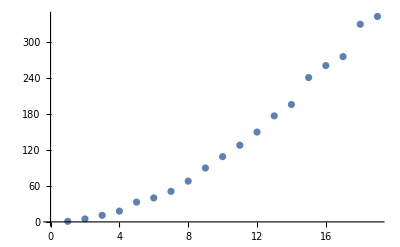

```mathematica
ListPlot[mass/@evolveTrace[dna,18][board]]
```